```mathematica
CycleGraph[2]
```

-Graphics-

```mathematica
ClawGraph[n_]:=Graph[Table[1<->k,{k,2,n}]]
```

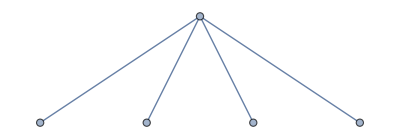

```mathematica
ClawGraph[5]
```

```mathematica
Table[Length[ListofVars[FindEmptyFormula[CycleGraph[k]]]],{k,2,8}]
```

{2,5,12,27,58,121,248}

```mathematica
Table[Length[ListofVars[FindFullFormula[CycleGraph[k]]]],{k,3,8}]
```

{1,4,11,41,162,715}

```mathematica
Table[Length[ListofVars[FindEmptyFormula[ClawGraph[k]]]],{k,2,8}]
```

{2,4,8,16,32,64,128}

```mathematica
Table[Length[ListofVars[FindFullFormula[ClawGraph[k]]]],{k,2,8}]
```

{1,2,5,15,52,203,877}

```mathematica
Table[2^n-n,{n,3,15}]
```

{5,12,27,58,121,248,503,1014,2037,4084,8179,16370,32753}

```mathematica
Table[Length[ListofVars[FindEmptyFormula[CompleteGraph[k]]]],{k,3,6}]
```

{5,15,52,203}

```mathematica
Table[Length[ListofVars[FindFullFormula[CompleteGraph[k]]]],{k,3,6}]
```

{1,1,1,1}

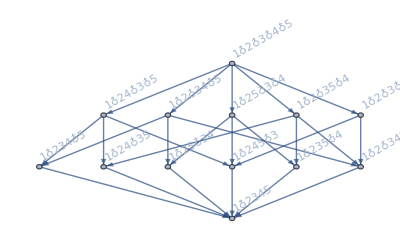
-Graphics-→-Graphics-1213

```mathematica
With[{k=121},
Graph[FormulaGraphReverse2[allGraphs5[k,"graph"]//FindEmptyFormula],ImageSize->400]->ShowGraph5Least[k]
]
```

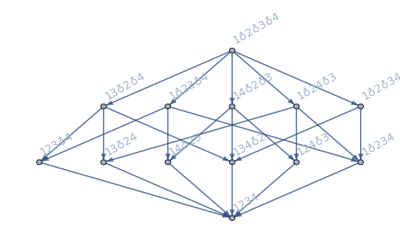
-Graphics-→-Graphics-

```mathematica
With[{k=121},
Graph[FormulaGraphReverse2[allGraphs4[k,"graph"]//FindEmptyFormula],ImageSize->400]->allGraphs4[k,"graph"]
]
```

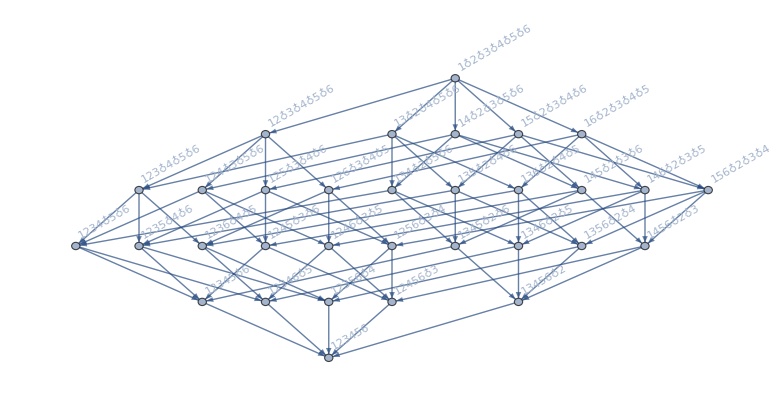
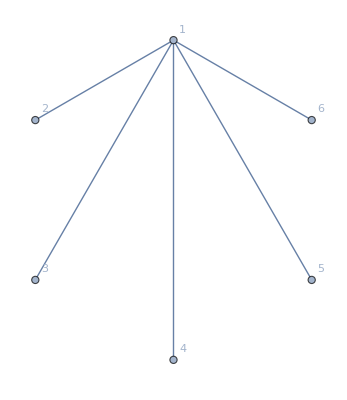
-Graphics-→-Graphics-

```mathematica
With[{g=ClawGraph[6]},
Graph[FormulaGraphReverse2[g//FindEmptyFormula],ImageSize->400]->g
]
```